```mathematica
s=InputString["Enter xml file name","engine_visibility_saliency.xml"]//StringReplace[#," "->""]&;
xml=Import[NotebookDirectory[]<>s];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},path}=xml;
Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]
```

D:\document\work\artivvis-development-repository\data\engine.tfi
D:\_volume_data\Mathematica\CTengine.tiff
{Feature 1,Feature 2,Feature 3,Feature 4}
front
{D:\document\work\time-varying-visualization\~images\engine_saliency_chart.png,D:\document\work\time-varying-visualization\~images\engine_visibility_chart.png,D:\document\work\time-varying-visualization\~images\engine_visibility_saliency_brightness_chart.png,D:\document\work\time-varying-visualization\~images\engine_visibility_saliency_saturation_chart.png,D:\document\work\time-varying-visualization\~images\engine_visibility_saliency_weighted_chart.png}
{D:\document\work\time-varying-visualization\~images\engine_saliency_chart.txt,D:\document\work\time-varying-visualization\~images\engine_visibility_chart.txt,D:\document\work\time-varying-visualization\~images\engine_visibility_saliency_brightness_chart.txt,D:\document\work\time-varying-visualization\~images\engine_visibility_saliency_saturation_chart.txt,D:\document\work\time-varying-visualization\~images\engine_visibility_saliency_weighted_chart.txt}
{D:\document\work\time-varying-visualization\~images\engine_visibility_saliency_feature.png,D:\document\work\time-varying-visualization\~images\engine_visibility.raw}
D:\document\work\time-varying-visualization\~images\

```mathematica
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
```

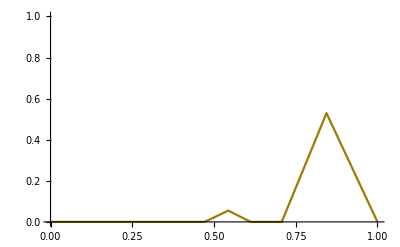

```mathematica
intensity0=intensity;
alpha0=alpha;
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0]];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]
```

```mathematica
d = Import[volumefile,"Image3D"];
dtf=Image3D[d,ColorFunction->rgbafunction]
```

-Graphics3D-

```mathematica
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]];
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]];
(*g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
```

```mathematica
pos=intensity[[#]]&/@Position[alpha,_?(#==0&)];
features=Table[ImageApply[If[#≥First[pos[[i]]] && #≤First[pos[[i+1]]],1,0]&,d],{i,1,Length[pos],2}]
chartcolors=rgbcolors[[#]]&/@Position[alpha,_?(#>0&)]//Flatten
```

{-Graphics3D-,-Graphics3D-}

{RGBColor[{1., 0., 0.}],RGBColor[{0.28627450980392155, 1., 0.00392156862745098}]}

```mathematica
top:=Module[{list,count,img,list2,list3,tmp},(* top *)
list=Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
```

```mathematica
back:=Module[{list,count,img,list2,list3,tmp},(* back *)
list=Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
```

```mathematica
left:=Module[{list,count,img,list2,list3,tmp},(* left *)
list=Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
```

```mathematica
bottom:=Module[{list,count,img,list2,list3,tmp},(* bottom *)
list=Reverse@Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
```

```mathematica
front:=Module[{list,count,img,list2,list3,tmp},(* front *)
list=Reverse@Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
```

```mathematica
right:=Module[{list,count,img,list2,list3,tmp},(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
```

```mathematica
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
vis=renderslices[face]
```

-Graphics3D-

{0.852149,0.147851}

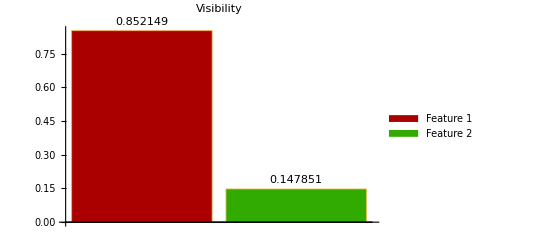

{0.175858,0.473708}

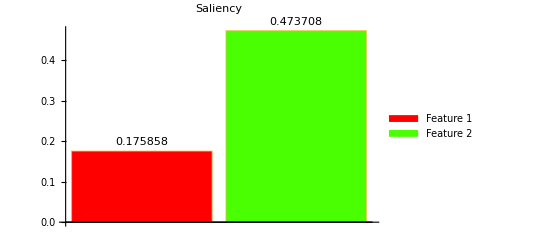

{0.0852765,0.914723}

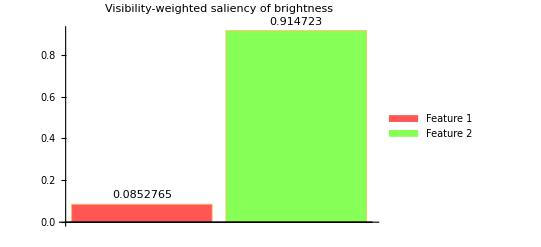

{0.0742732,0.925727}

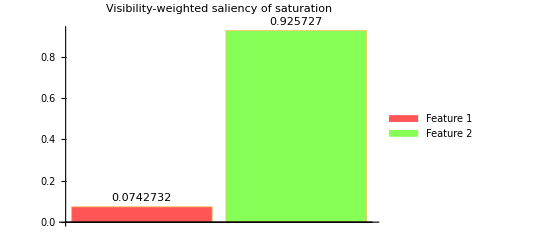

{0.0797749,0.920225}

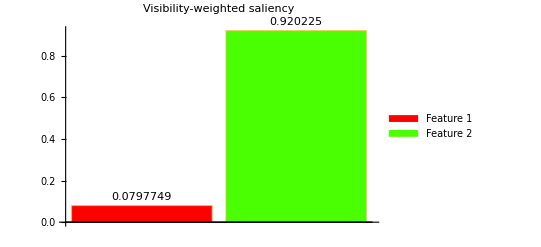

```mathematica
visibility=Table[ImageMeasurements[ImageMultiply[vis,features[[i]]],"TotalIntensity"]/ImageMeasurements[vis,"TotalIntensity"],{i,Length[features]}]
chart1=BarChart[visibility,PlotLabel->"Visibility",ChartLegends->legends,ChartStyle->(chartcolors//Darker),ChartLabels->Placed[ToString/@visibility,Above]]
dog=g1;
saliency=Table[ImageMeasurements[ImageMultiply[dog,features[[i]]],"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"],{i,Length[features]}]
chart0=BarChart[saliency,PlotLabel->"Saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@saliency,Above]]
viss=ImageMultiply[dog,vis];
vs=Table[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}]
chart2=BarChart[vs,PlotLabel->"Visibility-weighted saliency of brightness",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs,Above]]
viss2=ImageMultiply[g2,vis];
vs2=Table[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}]
chart2b=BarChart[vs2,PlotLabel->"Visibility-weighted saliency of saturation",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs2,Above]]
mean=Mean[{vs,vs2}]
weighted=BarChart[mean,PlotLabel->"Visibility-weighted saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@mean,Above]]
```

```mathematica
charts={chart0,chart1,chart2,chart2b,weighted};
scores={saliency,visibility,vs,vs2,mean};
Table[Export[imagefilenames[[i]],charts[[i]]],{i,Length[charts]}];
Table[Export[txtfilenames[[i]],scores[[i]]],{i,Length[scores]}];
```

```mathematica
w=ImageAdd[viss,viss2]//ImageAdjust;
results=ImageMultiply[w,#]&/@features;
MapIndexed[Export[StringReplace[featurefilename,"."->ToString[First[#2]]<>"."],#]&,results];
```

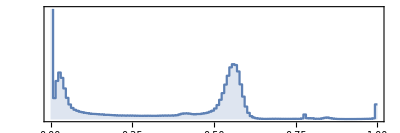

```mathematica
Export[visibilityfilename,Flatten@ImageData[vis,"Byte"],{"Binary","Byte"}];
ImageHistogram[d]
```

```mathematica
(*Export[path<>"Tooth_RGBA.raw",Flatten@ImageData[r,"Byte"],{"Binary","Byte"}];
Export[path<>"Tooth_"<>StringTake["RGBA",{#}]<>".raw",Flatten@ImageData[ColorSeparate[r,"RGBA"][[#]],"Byte"],{"Binary","Byte"}]&/@Range[4];
s="NDims = 3
DimSize = 140 120 161
ElementType = MET_UCHAR
ElementSpacing = 1.0 1.0 1.0
ElementByteOrderMSB = False
ElementDataFile = Tooth_.raw\n";
Export[path<>"Tooth_"<>StringTake["RGBA",{#}]<>".mhd",StringReplace[s,"Tooth_"->"Tooth_"<>StringTake["RGBA",{#}]],"Text"]&/@Range[4];*)
```